```mathematica
(*4.2*)
(*Calculate analytically the Renyi dimension spectrum Subscript[D, q] of the weighted Cantor set. Make sure that for q=0 you recover the box counting dimension of the Cantor set*)
```

```mathematica
(*
The general formula of Rényi dimension spectrum is;
Subscript[D, q] = 1/(1-q) lim_(ϵ->0) (ln(Subscript[I, q](ϵ)))/(ln(1/ϵ)) (eq.1); 
where;
Subscript[I, q](ϵ) = ∑_(j=1)^Subscript[N, box] Subscript[P, j]^q(ϵ) (eq.2);
Subscript[P, j](ϵ) = (Subscript[N, j](ϵ))/Subscript[N, total] (eq.3); (Subscript[P, j](ϵ)-> the fraction of points in the j:th box of size ϵ);
                (Subscript[N, j](ϵ) -> number of points in the j:th box of size ϵ);
To obtain Subscript[D, q] we need to first compute Subscript[P, j](ϵ);
We can look at the figure to find a pattern. The pattern that can be discerned in the figure is that the right side is doubled while the left side remain the same.;
We can visualize this like a P and 1-P for the first level; We can now find expressions for all the levels(L);

L 0 - no expression;
L 1      P               1-P;
L 2   P^2  P(1-P)   P(1-P)  (1-P)^2;

L 2 - can be rewritten to;
L 2   P^2              2P(1-P)             (1-P)^2;
L 3 P^3 P^2(1-P)  2 P^2(1-P)  2P(1-P)^2   P(1-P)^2 (1-P)^3;

L 3 - can also be rewritten as;
L 3 P^3   3 P^2(1-P)   3P(1-P)^2   (1-P)^3;

By looking at level 3 we can see that the pattern is Pascal's triangle and Binomial Coefficient;Subscript[P, j](ϵ) = P^k(1-P)^(n-k) with n = the level & multiplicity is given by binomial coefficient;
We can now replace (eq.2)to;
Subscript[I, q](ϵ) = ∑_(k=1)^n Binomial(n,k) * (P^k(1-P)^(n-k))^q;
We have now obtained an expression in terms of q and can solve the rest in mathematica*)
```

```mathematica
P = 1/3;
ϵ = 3^-n;
Subscript[I, q]=FullSimplify[Sum[Binomial[n,k]*(P^k(1-P)^(n-k))^q,{k,1,n}]];
Subscript[D, q]=1/(1-q) Limit[ Log[Subscript[I, q]]/Log[1/ϵ],{n->Infinity}];
expr = Numerator[Subscript[D, q][[1]]];
s = FullSimplify@Log@Exp[expr]
```

Log[3^-q (1+2^q)]

```mathematica
(* The answer above can be rewritten as ;
Log[(1/3)^q + (2/3)^q];

And we can now insert this in the original Subscript[D, q];

Subscript[D, q] = Log[(1/3)^q + (2/3)^q]/((1-q)Log[3]) = 1/(1-q)*Log[(1/3)^q + (2/3)^q]/Log[3];

Lastly we can check if q=0;
Subscript[D, q] = 1/(1-0)*Log[1 + 1]/Log[3] = Log[2]/Log[3]; -> the box counting dimension of the Cantor set
so the answer is -> Subscript[D, q] = 1/(1-q)*Log[(1/3)^q + (2/3)^q]/Log[3];
*)
```

```mathematica
(*4.2b*)
(*Using the expression derived in (a) make a plot of Subscript[D, q] as a function of q for q∈[−20,20].*)
```

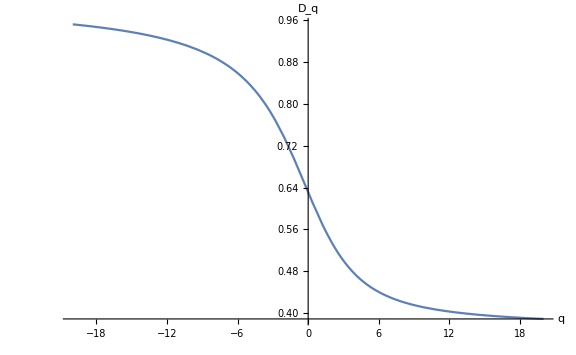

```mathematica
Subscript[D, q2]=1/(1-q)*Log[(1/3)^q + (2/3)^q]/Log[3];
Plot[Subscript[D, q2],{q,-20,20}, AxesLabel->{"q","D_q"}]
```

```mathematica
(*4.2c*)(*Note: log in mathematica is the natural logarithm ln*)
(*Using the expression derived in (a) compute explicitly (D​)_1 (information dimension) and Subscript[D, 2](correlation dimension) of the weighted Cantor set.*)
```

```mathematica
s1= {Limit[Subscript[D, q2],{q->1}], Limit[Subscript[D, q2],{q->2}]}
```

{Log[27/4]/Log[27],Log[9/5]/Log[3]}

```mathematica
(*4.2d*)
(*Using the expression derived in (a),compute explicitly D(.08)_(−∞​​)​=lim_(q->−∞) D(.08)_q and D(.08)_(∞​​)​​​=lim_(q->∞) D(.08)_q of the weighted Cantor set.*)
```

```mathematica
s2 = {Limit[Subscript[D, q2],{q->-∞}], Limit[Subscript[D, q2],{q->∞}]}
```

{1,Log[3/2]/Log[3]}